# HW 3 - ASTR 503 Created with Wolfram Mathematica 11.0 on 9-16-2016

## Daniel George - dgeorge5@illinois.edu

## Step 1

```mathematica
n=2048; (*Sample rate*)
```

We normalize all noises to have a standard deviation of 1.

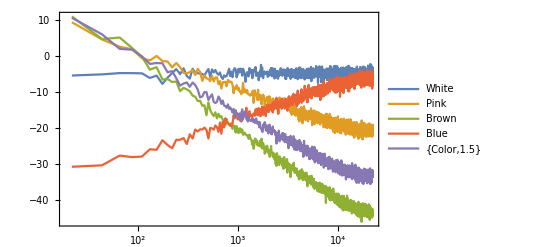

```mathematica
Periodogram[AudioGenerator/@(n={"White","Pink","Brown","Blue",{"Color",1.5}}),2000,ScalingFunctions->{"Log10","dB"},PlotLegends->Placed[n,Right],Frame->True]
```

## White noise

```mathematica
white=#/StandardDeviation@#&@RandomVariate[NormalDistribution[],2n];
```

### Counts above 3σ

```mathematica
Length@Select[white-Mean@white,Abs@#≥3&]
```

10

## Pink noise

```mathematica
pink=#/StandardDeviation@#&@Take[Fourier@Join[{0.},#,{0.},Reverse@Conjugate@#]&[(Range[1. #]^-.5RandomVariate[NormalDistribution[],#]*RandomPoint[Circle[],#]&[2n]).{1.,I}]//Chop,2n];
```

### Counts above 3σ

```mathematica
Length@Select[pink-Mean@pink,Abs@#≥3&]
```

9

## Brownian noise

```mathematica
brown=#/StandardDeviation@#&@Accumulate@RandomVariate[NormalDistribution[],2n ];
```

### Counts above 3σ

```mathematica
Length@Select[brown-Mean@brown,Abs@#≥3&]
```

0

Thus we can see that the counts above σ is maximum for white and minimum for brown noise. This is expected because the drift increases as we move from white to pink to brown noise.

## 5.5Hz sinusoidal signal

```mathematica
sin5p5=4.Sin[2.Pi 5.5 Most@Range[0.,2,1./n]+2Pi RandomReal[]];
```

## Dirty 60Hz signal

```mathematica
dirty60=2. Sin@Round[2.Pi 60Most@Range[0.,2,1./n]+2Pi RandomReal[],10.^-2];
```

## Total signal

```mathematica
list={dirty60,sin5p5,white,brown,pink}; AppendTo[list,sum=Total@list];
```

## Time series plots

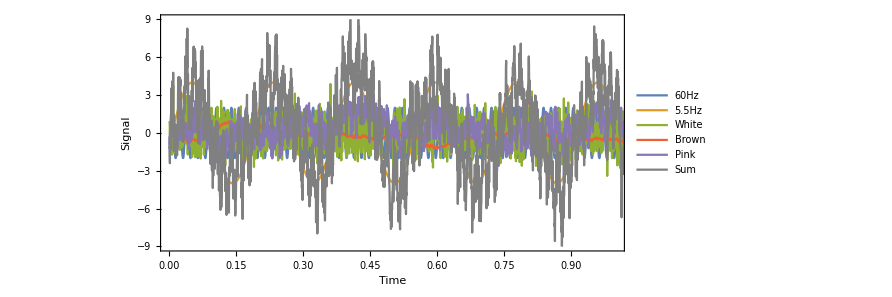

```mathematica
ListLinePlot[list[[All,;;2n]],DataRange->{0,2-1./n},Frame->True,PlotStyle->{Thin,Thick,Thin,Thick,Medium,{Thin,Gray}},ImageSize->660,AspectRatio->.45,PlotRange->{{0,1},{-9,9}},PlotLegends->Placed[{"60Hz","5.5Hz","White","Brown","Pink","Sum"},Above],FrameLabel->{"Time","Signal"}]
```

## Step 2

## Power spectrum of different noises

### Finding power law fits to each periodogram

```mathematica
fits=LinearModelFit[Log@Transpose@{Range[1.,n/4],Take[PeriodogramArray[#[[;;n]]],n/4]},{x},x]&/@{white,brown,pink};
```

### Slopes of best fit lines and their errors

```mathematica
Insert[#,"±",3]&/@(Join[{{"α(White) =","α(Brown) =","α(Pink)  ="}},(Through@#)[[All,2]]&/@fits/@{"BestFitParameters","ParameterErrors"}]//Transpose)//Grid
```

α(White) = | 0.00123843 | ± | 0.0584904
α(Brown) = | -2.02745 | ± | 0.0538668
α(Pink)  = | -1.03939 | ± | 0.0609803

## Spectral power density plots

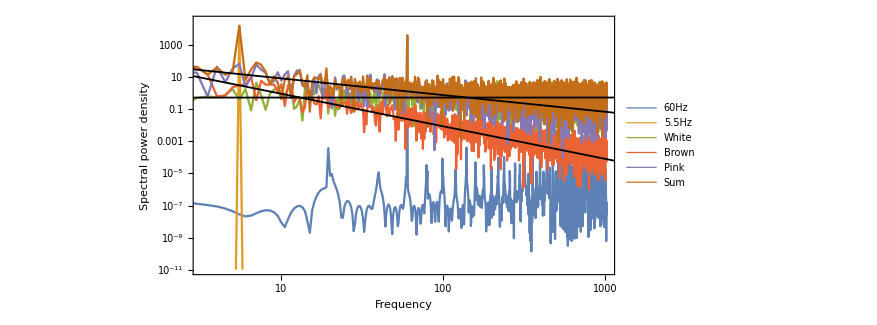

```mathematica
Show[Periodogram[list,Frame->True,ImageSize->650,AspectRatio->.5,PlotStyle->Thickness[.0025],PlotRange->{{3.2,n/2},{10^-11,10^4.5}},ScalingFunctions->{"Log","Log"},SampleRate->n ,FrameLabel->{"Frequency","Spectral power density"},PlotLegends->Placed[{"60Hz","5.5Hz","White","Brown","Pink","Sum"},Above]],LogLogPlot[E^fits[[#]]@Log[x]&/@Range[3]//Evaluate,{x,0,n},PlotStyle->{{Black,Thickness[.002]}}]]
```

## Step 3

## High & low pass filters (300Hz, 10Hz)

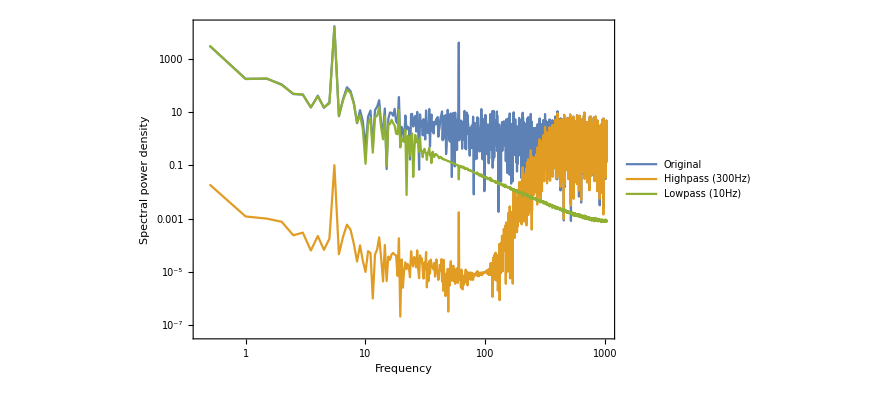

```mathematica
Periodogram[{sum,HighpassFilter[sum,300 2 Pi,SampleRate-> n],LowpassFilter[sum,10 2Pi ,SampleRate->n]},SampleRate->n,PlotRange->All,ScalingFunctions->{"Log","Log"},Frame->True,ImageSize->650,PlotLegends->Placed[{"Original","Highpass (300Hz)","Lowpass (10Hz)"},Above],FrameLabel->{"Frequency","Spectral power density"}]
```

## Extracting the signal

### Plotting the cross-correlation of the signal with itself

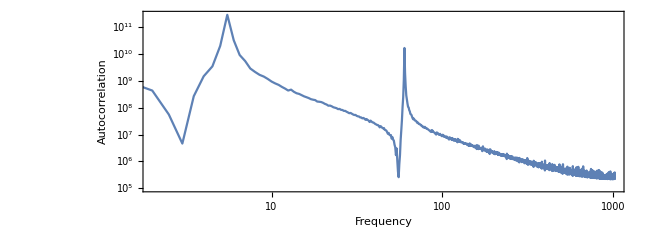

```mathematica
Periodogram[aCorr=ListCorrelate[sum,sum,{1,1},0],ScalingFunctions->{"Log","Log"},SampleRate->n,Frame->True,AspectRatio->.35,ImageSize->650,PlotRange->{{2,n/2},All},FrameLabel->{"Frequency","Autocorrelation"}]
```

### Finding the largest peaks

```mathematica
(Reverse[SortBy[FindPeaks[PeriodogramArray[aCorr][[3;;n]]],Last]][[1;;2,1]]+1.)/2"Hz"
```

{5.5 Hz,60. Hz}

### Applying bandpass filter from 5Hz to 6Hz

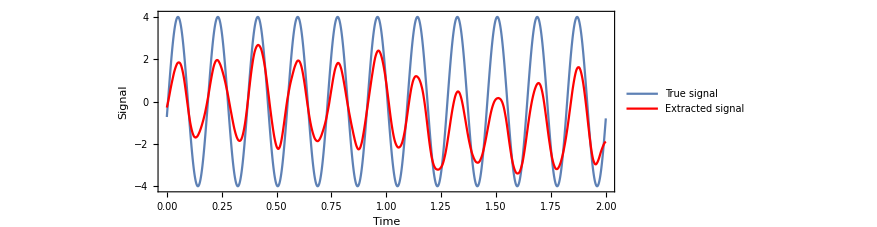

```mathematica
ListLinePlot[{sin5p5,LowpassFilter[HighpassFilter[sum,2Pi 5,SampleRate->n],2Pi 6,SampleRate->n]},Frame->True,PlotRange->{-4.1,4.1},PlotStyle->{{Medium},{Red,Thick}},DataRange->{0,2},AspectRatio->.35,ImageSize->650,PlotLegends->Placed[{"True signal","Extracted signal"},Above],FrameLabel->{"Time","Signal"}]
```